## Question 6

```mathematica
trace=RightComposition[fname↦FileNameJoin["D:\\gw\\DTS207TC\\cw2\\",fname],
path↦ReadList[path,Number,RecordSeparators->{","}]
]/@{"trace1.txt","trace2.txt"};
```

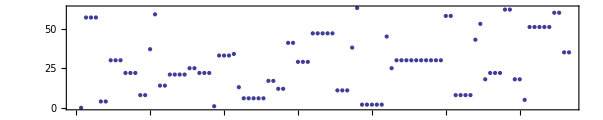

D:\gw\DTS207TC\trace1-100.png

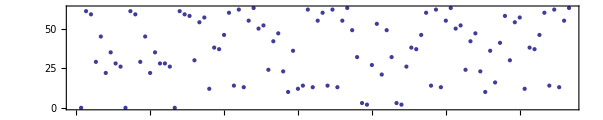

D:\gw\DTS207TC\trace2-100.png

```mathematica
g=ListPlot[trace[[1,;;100]],AspectRatio->1/5,PlotStyle->PointSize[Small],PlotTheme->{"Classic","Frame"}]
Export["D:\\gw\\DTS207TC\\trace1-100.png",g,Background->None]
g=ListPlot[trace[[2,;;100]],AspectRatio->1/5,PlotStyle->PointSize[Small],PlotTheme->{"Classic","Frame"}]
Export["D:\\gw\\DTS207TC\\trace2-100.png",g,Background->None]
```

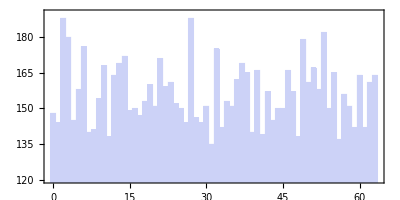

D:\gw\DTS207TC\trace2-hist.png

```mathematica
g=Histogram[trace[[2]],64,PlotTheme->{"Classic","Frame"},AspectRatio->1/2,PlotRange->{120,190}]
Export["D:\\gw\\DTS207TC\\trace2-hist.png",g,Background->None]
```

```mathematica
SortBy[Tally[trace[[2]]],Last]
```

{{31,135},{56,137},{11,138},{48,138},{41,139},{7,140},{39,140},{8,141},{33,142},{59,142},{61,142},{1,144},{26,144},{29,144},{4,145},{43,145},{28,146},{17,147},{0,148},{15,149},{16,150},{25,150},{44,150},{45,150},{54,150},{20,151},{30,151},{35,151},{58,151},{24,152},{18,153},{34,153},{9,154},{57,156},{42,157},{47,157},{5,158},{52,158},{22,159},{19,160},{23,161},{50,161},{62,161},{36,162},{12,164},{60,164},{63,164},{38,165},{55,165},{40,166},{46,166},{51,167},{10,168},{13,169},{37,169},{21,171},{14,172},{32,175},{6,176},{49,179},{3,180},{53,182},{2,188},{27,188}}

```mathematica
1/64.
```

0.015625